# PHAS2443: Practical Mathematics II Exercises 2: Convolutions and Images Model Solutions

1. This exercise explores the accuracy of approximations to derivatives. Look at the three functions
   a)   Exp[-x]
   b)  Sin[x]
   c)  Log[x]
   and consider their derivatives in the range 0.01<x<2π.
   For each function use graphs to compare 
   i) the exact derivative
   ii) the 'forward difference' approximation, df/dt≈(f(t+δt)-f(t))/δt
   iii) the 'backward difference' approximation, df/dt≈(f(t)-f(t-δt))/δt
   iv) the 'centred difference' approximation,  df/dt≈(f(t+δt)-f(t-δt))/(2 δt).
   Try to use efficient methods for implementing the derivatives.
   Experiment with various values of the finite difference, δt.  Can you draw any general conclusions about the relative accuracies of the one-sided and centred differences?

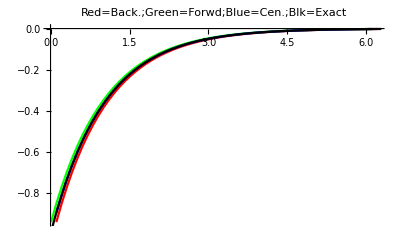

```mathematica
dback[f_,min_,max_,δx_]:=Module[{t},t=Table[f,{x,min,max,δx}];ListPlot[Rest[Transpose[{Table[x,{x,min,max,δx}],(t-RotateRight[t])/δx}]],PlotRange->All,Joined->True,PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity]]
dfor[f_,min_,max_,δx_]:=Module[{t},t=Table[f,{x,min,max,δx}];ListPlot[Drop[Transpose[{Table[x,{x,min,max,δx}],(RotateLeft[t]-t)/δx}],-1],PlotRange->All,Joined->True,PlotStyle->RGBColor[0,1,0],DisplayFunction->Identity]]
dcentred[f_,min_,max_,δx_]:=Module[{t},t=Table[f,{x,min,max,δx}];ListPlot[Drop[Rest[Transpose[{Table[x,{x,min,max,δx}],(RotateLeft[t]-RotateRight[t])/(2 δx)}]],-1],PlotRange->All,Joined->True,PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity]]
p1=dback[ⅇ^-x,0.01,2 π,0.1];
p2=dfor[ⅇ^-x,0.01,2 π,0.1];
p3=dcentred[ⅇ^-x,0.01,2 π,0.1];
p4=Plot[-ⅇ^-x,{x,0.01,2 π},DisplayFunction->Identity,PlotStyle->RGBColor[0,0,0]];
Show[p1,p2,p3,p4,PlotLabel->"Red=Back.;Green=Forwd;Blue=Cen.;Blk=Exact"]
```

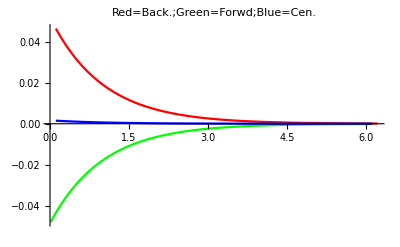

```mathematica
ddback[f_,min_,max_,δx_]:=Module[{t,dt,xx},t=Table[f,{x,min,max,δx}];dt=Table[D[f, x]/.x->xx,{xx,min,max,δx}];ListPlot[Rest[Transpose[{Table[x,{x,min,max,δx}],dt-(t-RotateRight[t])/δx}]],PlotRange->All,Joined->True,PlotStyle->RGBColor[1,0,0]]]
ddfor[f_,min_,max_,δx_]:=Module[{t,dt,xx},t=Table[f,{x,min,max,δx}];dt=Table[D[f, x]/.x->xx,{xx,min,max,δx}];ListPlot[Drop[Transpose[{Table[x,{x,min,max,δx}],dt-(RotateLeft[t]-t)/δx}],-1],PlotRange->All,Joined->True,PlotStyle->RGBColor[0,1,0]]]
ddcentred[f_,min_,max_,δx_]:=Module[{t,dt,xx},t=Table[f,{x,min,max,δx}];dt=Table[D[f, x]/.x->xx,{xx,min,max,δx}];ListPlot[Drop[Rest[Transpose[{Table[x,{x,min,max,δx}],dt-(RotateLeft[t]-RotateRight[t])/(2 δx)}]],-1],PlotRange->All,Joined->True,PlotStyle->RGBColor[0,0,1]]]
fpl[f_,δ_]:=Show[ddback[f,0.01,2 π,δ],ddfor[f,0.01,2 π,δ],ddcentred[f,0.01,2 π,δ],PlotLabel->"Red=Back.;Green=Forwd;Blue=Cen.",PlotRange->All]
fpl[ⅇ^-x,0.1]
```

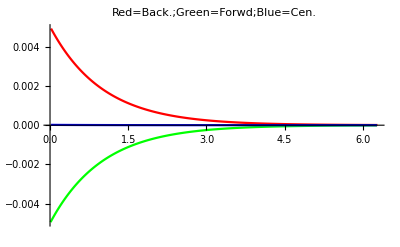

```mathematica
fpl[Exp[-x],.01]
```

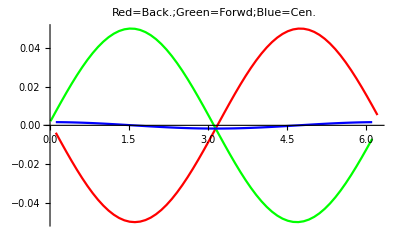

```mathematica
fpl[Sin[x],.1]
```

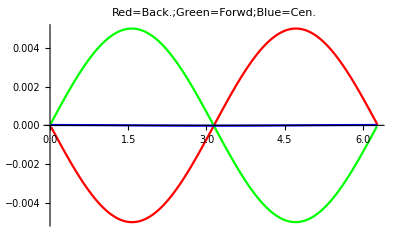

```mathematica
fpl[Sin[x],.01]
```

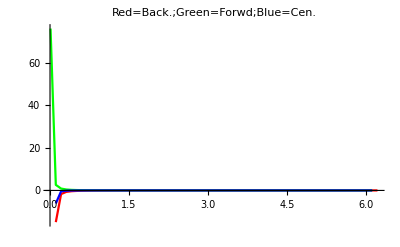

```mathematica
fpl[Log[x],.1]
```

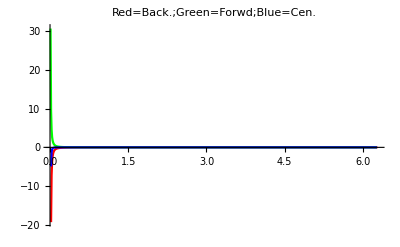

```mathematica
fpl[Log[x],.01]
```

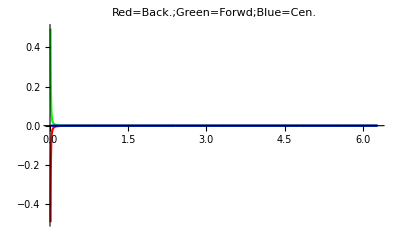

```mathematica
fpl[Log[x],.0001]
```

COMMENT: What should emerge is that the centred difference method is better -- in fact, if one looks carefully at, for example, the sin case the difference between the one-sided and centred gets more marked as the step length changes. The centred difference form is accurate to a higher order than the one-sided form. We shall explore this in more detail in Lecture 3.

2. This problem involves setting up a simple one-dimensional model of diffusion. Imagine that space is divided up into a finite number of positions, and that on each tick of the clock a particle at any position has a probability p of moving to an adjacent position, with equal probability of moving to the left or to the right. For position i, then, if the numbers of particles at i and its neighbours are  n_(i-1), n_i and n_(i+1),  at the next time step the number of particles at i will be  (p/2 n_(i-1)+(1-p) n_i + p/2 n_(i+1)). We will assume that particles may be divided, and treat the ns as real numbers.  
  Write Mathematica code to model this behaviour, using either RotateRight and RotateLeft or ListConvolve, and apply it to a system of 101 positions, initially empty except for 100 particles in cell 51. With p=0.1, run the sumilation for 500 time steps and plot the result.
   Investigate what happens with the same system when a bias is applied, so that the probability of moving to the right is 0.055 and to the left 0.045.

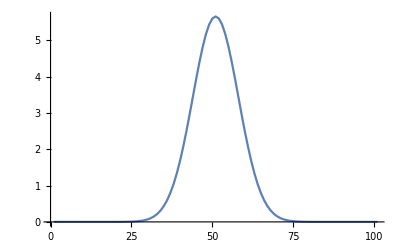

```mathematica
init=Table[0,{101}];
init⟦51⟧=100;
s1[ar_List,p_]:=0.5 p RotateRight[ar]+(1-p) ar+0.5 p RotateLeft[ar]
p1=ListPlot[Nest[s1[#1,0.1]&,init,500],Joined->True,PlotRange->All]
```

For completeness, let' s tackle the same problem using ListConvolve. Now the convolution "window" is just three cells wide, and it picks up the cells with weights (for the unsymmetrical case) .055, .9, .045.

```mathematica
s2[ar_List,p_]:=ListConvolve[{0.5 p,1-p,0.5 p},ar,2,{0}]
p2=ListPlot[Nest[s2[#1,0.1]&,init,500],Joined->True,PlotRange->All]
```

-Graphics-

As a check, overlay the plots from the rotation method and the convolution method.

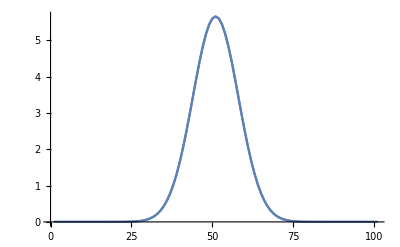

```mathematica
Show[p1,p2]
```

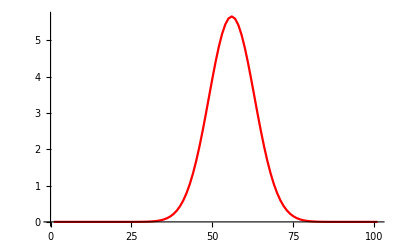

```mathematica
s1b[ar_List,pr_,pl_]:=pr RotateRight[ar]+(1-pl-pr) ar+pl RotateLeft[ar]
p3=ListPlot[Nest[s1b[#1,0.055,0.045]&,init,500],Joined->True,PlotRange->All,PlotStyle->RGBColor[1,0,0]]
```

Check the difference between the symmetrical and the biased diffusion

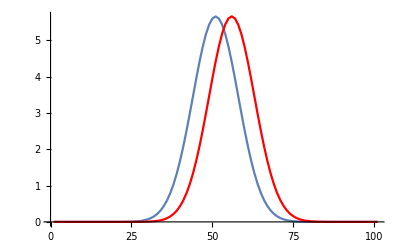

```mathematica
Show[p1,p3]
```

Note that in the final figure the material spreads out as its centre of gravity drifts sideways.

3. This problem sets up a demonstration of the Rayleigh criterion for the separation of images. The criterion depends on the diffraction pattern of a circular aperture: the intensity in a beam at an angle θ from the normal to an aperture of radius a is
    I(θ)=((2J_1(k a Sin(θ)))/(k a Sin(θ)) )^2 
where k is the wavevector of the light and J_1 is the first order Bessel function of the first kind (BesselJ).
   First create an ideal image. This should be a series of one-unit spikes, at varying spacngs. Create a 255 by 255 grid, with one spike at the centre, and at the corners and  centres of edges of squares, centred on the centre, with edges of lengths 8, 16, 32, 64, 128.
   Now set up a square array, 40 by 40, to represent the blurring arising from this function. Take ka=200, and calculate θ assuming that the image is 2000 units from the aperture, and that the spacing of the mesh is 1 unit. First plot your blur function, then convolve it with the image. 
      Comment on whether your impression of the resulting blurred image is consistent with Rayleigh's criterion, which states that two images can be resolved if their angular separation is greater than 1.22 λ/d where d is the diameter of the aperture and λ is the wavelength.

```mathematica
ims=255;imh=128;image=Table[0,{ims},{ims}];
image⟦imh,imh⟧=1
Do[i=2^j;image⟦imh+i,imh⟧=1;image⟦imh-i,imh⟧=1;image⟦imh,imh+i⟧=1;image⟦imh,imh-i⟧=1;image⟦imh+i,imh+i⟧=1;image⟦imh+i,imh-i⟧=1;image⟦imh-i,imh+i⟧=1;image⟦imh-i,imh-i⟧=1,{j,2,6}];
ListDensityPlot[image,Mesh->False]
```

1

-Graphics-

```mathematica
range=2000; ka=200;

(* Note there is a singularity in the blur function at x=y=0, but the limit is meaningful: *)
Limit[Limit[(2 BesselJ[1,ka Sqrt[x^2+y^2]/range]/(ka Sqrt[x^2+y^2]/range))^2,x->0],y->0]
```

1

```mathematica
(* Set up function definition to take this into account at x=y=0 *)
blur[0.,0.]:=1.;
blur[x_,y_]:=(2 BesselJ[1,ka Sqrt[x^2+y^2]/range]/(ka Sqrt[x^2+y^2]/range))^2

Plot3D[blur[x,y],{x,-20,20},{y,-20,20},PlotRange->All]
```

-Graphics3D-

```mathematica
blurt=Table[blur[x,y],{x,-20.,20.},{y,-20.,20.}];
blurim=ListConvolve[blurt,image,{-1,1},{0}];
ListDensityPlot[blurim,Mesh->False]
```

-Graphics-

Comment: it looks as if we can just about separate the bright spot at a distance of 64 from that at 32, very easily separate that at 64 √2 from that at 32 √2, just about separate that at 32 √2 from that at 16 √2. The angular separation is thus about 16√2/2000=0.022. We also know that k a = 200, so λ/d = (2π/k)/d=π/(k a) = π/200=0.016. It looks, then, as if the Rayleigh criterion is about right.

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009, January 2011,January 2017, January 2018.